## Notes

This program extracts Apple Health data (.csv format)  and graphs and analyzes heart rate data.

## Inputting, Formatting, and Extracting Useful Data from File

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Connie\Downloads\Summer2018Starter-master\Summer2018Starter-master\Summer2018

```mathematica
heartRate= Import["HKQuantityTypeIdentifierHeartRate.csv","CSV"];
```

```mathematica
(* extracts last column of data (heart rate)*)
getImportantData[ entries_List ]:= Part[ entries , All, -1];

(* gets second to last column in the data (time) *)
getDateString[ entry_String ]:= Part [ StringSplit[ entry ,";"] , -2] ;

(* gets 2nd to last column of data which is heart rate value as a Number *)
getHeartRate[ entry_String ]:= ToExpression [Part [ StringSplit[ entry ,";"] , -1]] ;
```

```mathematica
(* example: *)
```

```mathematica
getDateString ["software:3.1>;count/min;2017-02-06 20:00:03 -0400;2017-02-06 19:58:53 -0400;2017-02-06 19:58:53 -0400;61"]
```

2017-02-06 19:58:53 -0400

```mathematica
(* Dropping the first line, extract all rows and columns of heartrate data: *)
```

```mathematica
getImportantData[Drop[heartRate,1]]
```

{software:3.1>;count/min;2017-02-06 20:00:03 -0400;2017-02-06 19:58:53 -0400;2017-02-06 19:58:53 -0400;61,software:3.1>;count/min;2017-02-06 20:05:12 -0400;2017-02-06 20:03:21 -0400;2017-02-06 20:03:21 -0400;60,257625,software:4.3.1>;count/min;2018-07-04 14:30:46 -0400;2018-07-04 14:25:36 -0400;2018-07-04 14:25:36 -0400;71}
 |  |  |  |

```mathematica
(* Put in one time entry as formatted by apple watch, output DateObject to use to plot Mathematica *)
 getDateObject[ timeEntry_String ] := 
                                    With[ { extractTZ = StringTake[ timeEntry , {-5,-1} ]},
                                    
                                           (*timeZoneString = StringJoin[" GMT-", ToString[ (Interpreter["Number"][StringTake[extractTZ,{2,3}]])] ];*)
                                           
                                           DateObject[ StringDrop[ timeEntry , -5]
                                                         ]
                                         ];
                                         
  (* Apply getDateObject on all time datapoints *)
  (* Generate time column to plot heart rate data with *)
  getAllDateObjects [  entries_List ] := Map [ 
                                                 getDateObject[ 
                                                                getDateString [ # ]
                                                              ] &
                                                   ,
                                                   getImportantData[ entries ]
                                               ];
                                                   
 (* Generate heart rate column to plot *)
  getAllHeartPoints [  entries_List ] := Map [  
                                                getHeartRate
                                                , 
                                                getImportantData[ entries ] 
                                              ] ;
```

## Plot data

```mathematica
heartRatePoints = getAllHeartPoints [ Drop[heartRate,1]]
```

{61,60,58,61,55,53,52,51,49,49,49,49,49,49,51,51,52,53,54,54,54,59,61,51,51,51,50,51,52,52,53,53,49,51,54,52,53,52,49,49,49,52,53,51,51,51,52,58,57,50,51,51,53,54,54,50,49,51,51,52,51,49,52,94,51,54,61,51,62,57,257488,72,63,65,62,61,66,65,69,63,69,67,58,62,69,68,61,67,65,64,65,62,68,65,65,63,65,60,64,65,70,65,62,69,59,72,69,62,68,57,57,68,64,63,62,63,66,71,66,76,70,68,77,94,81,80,68,67,79,83,75,81,82,69,71,77,79,68,75,70,71}
 |  |  |  |

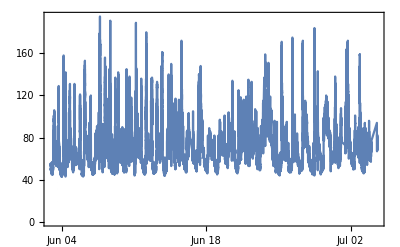

```mathematica
DateListPlot [ Take[Transpose[{dobjs,heartRatePoints}],-25000]]
```

```mathematica
dateObjects= %131 ;
```

```mathematica
dateObjects [[1]]
```

Mon 6 Feb 2017 19:58:53GMT-4.

Start From here

```mathematica
SetDirectory[NotebookDirectory []]
```

C:\Users\Connie\Downloads\Summer2018Starter-master\Summer2018Starter-master\Summer2018

```mathematica
Export ["DateObject.mx", dateObjects ,"MX" ]
```

DateObject.mx

```mathematica
dobjs=Import["DateObject.mx"];
```

```mathematica
getAllDateObjects[]
```

## Analysis

```mathematica
(* PLAN OUTLINE *)
```

```mathematica
(*________________ Part I: Look at irregular data: identify potential stress factors ____________________________*)
(* Exclude all data that falls within the range of healthy sample user (with options to choose age group and gender) *)
(* Identify instances of possible stress from times of out of range heart rate *)
(* Match up times of irregular heart rate with time of which activities were indicated from daily log *)
(* Purpose: allow people to increase their noninvasive retrospective self tracking capabilities *)
(* Emotions are one factor that determine heart rate :
 http://www.heart.org/HEARTORG/Conditions/HighBloodPressure/GettheFactsAboutHighBloodPressure/All-About-Heart-Rate-Pulse_UCM_438850_Article.jsp#.W0EdqbgnZEY
```

```mathematica
bin = CreateDatabin[];
```

```mathematica
CloudDeploy[FormFunction[{"id"->"Number","name"->"String","loc"->"Location"},(DatabinAdd[bin,<|"someData"->#id,"key"->#name,"Location"->#loc|>];
"Thanks for submitting your data to Hearty")&]]
```

CloudObject[https://www.wolframcloud.com/objects/99a2813e-86e1-4754-aba7-472f5304c54b]

```mathematica
Dataset[bin];
```

```mathematica
age= 27;
minTargetHeartrate = .50*(220-age)
maxTargetHeartrate = .85*(220-age)
```

96.5

164.05

```mathematica
getHealthyPoints[ heartrates_List, timestamps_List, minTargetHeartRate_, maxTargetHeartRate_]:= Module[{i, healthyPoints, currHeartRate},
	healthyPoints = {};

	For[i = 1, 
		i <= Length[heartrates], 
		i++,
		currHeartRate = heartrates⟦i⟧;
		If[currHeartRate < maxTargetHeartRate && currHeartRate > minTargetHeartRate,
			AppendTo[healthyPoints, {timestamps⟦i⟧, currHeartRate}]
		]
	];

	healthyPoints
]
```

```mathematica
targetHeartdata=getHealthyPoints[heartRatePoints, dobjs, minTargetHeartrate, maxTargetHeartrate]
```

{{Tue 7 Feb 2017 04:03:21GMT-4.,111},{Tue 7 Feb 2017 04:03:22GMT-4.,111},{Tue 7 Feb 2017 04:03:58GMT-4.,149},{Tue 7 Feb 2017 04:04:00GMT-4.,150},{Tue 7 Feb 2017 04:07:18GMT-4.,107},61219,{Mon 2 Jul 2018 23:07:04GMT-4.,104},{Mon 2 Jul 2018 23:07:13GMT-4.,99},{Mon 2 Jul 2018 23:07:16GMT-4.,97},{Mon 2 Jul 2018 23:07:28GMT-4.,98}}
 |  |  |  |

```mathematica
Export ["HealthyHeartData.mx", targetHeartdata ,"MX" ]
```

HealthyHeartData.mx

```mathematica
healthy=Import["HealthyHeartData.mx"];
```

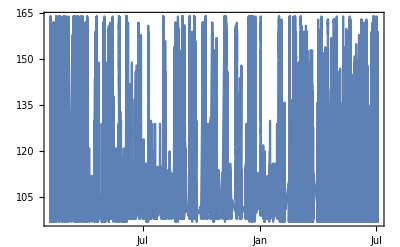

```mathematica
DateListPlot [targetHeartdata]
```

```mathematica
(*_________________ Part II: Determine resting heart rate: make exercise recommendations and print stats____________ *)
https://www.health.harvard.edu/blog/resting-heart-rate-can-reflect-current-future-health-201606179806
```

```mathematica
https://www.cdc.gov/physicalactivity/basics/measuring/heartrate.htm
```

!!!!!!!!!!!!!!!!!!!!!!!!!Get resting heart rate from input from website

```mathematica
testRHR = 95;
```

Subtract

```mathematica
(* Ask the user to follow instructions to determine his/her resting heart rate by following instructons and then inputting the number in a field on the website *)

(* _________________Part IB: Daily logs/questionaire answers_____________________________________________*)
(* Extract activities in log and moods*)
(* Make list of sentiments from using Classify functon on all sentences in each log *)
(* How to implement machine learning to learn moods and apply across the heart rate data *)
```

## Web Options

```mathematica
(* drop down menu for user to select age group and gender ?*)
```